# 28: Basic QR Algorithm

This (with some bells and whistles) is what almost all dense eigenvalue algorithms are based on after a preliminary reduction to upper Hessenberg (tridiagonal for symmetric) form. We are going to look at the scheme first and then work out why it works.

## Motivational Demo

The book says “Compute the QR decomposition, flip the order of the factors and repeat!”. Here is an example for a symmetric matrix.

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
TabView[
Table[
{Q,R}=QRDecomposition[T];Q=Qᵀ;
T=Chop[R.Q];
MatrixPlot[T],
{MaxIter}]
]
```

12345678910111213141516171819202122

Lets look at the first and last “T” matrices

```mathematica
TabView[{
"T_0"->MatrixForm[T0],
"T_1"->MatrixForm[T]}]
Eigenvalues[A]
```

12

{-4.63607,3.77096,2.95101,1.22294,-1.06596,-0.664728,-0.282256}

It is pretty clear that something is driving the off-diagonals to zero: this means the diagonals are heading to the eigenvalues!  We want to understand what is doing this. Once we understand that we might be able to make it go faster! In a fit of bravado, we are going to guess at something that makes it go faster

### Shifts

After a few steps I have a vague idea of some of the eigenvalues! There should be a way of incorporating these estimates into the algorithm.

Obvious Fact #42:
If the eigenvalues of A are {λ_1,λ_2,…,λ_m} then the eigenvalues of A-μ I_m are simply {λ_1-μ,λ_2-μ,…,λ_m-μ}
This is called a shift.

Less Obvious Observation:
If μ is an eigenvalue then one QR step on “T-μ I_m" makes the problem gets smaller. 
This is called “Deflation”.

{2.44012,1.28022,-3.86877,-0.179029,-2.72121,-0.905731,-1.56584}

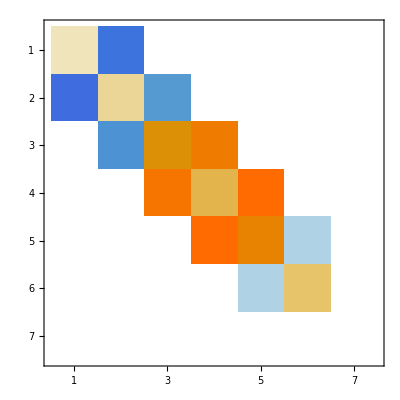

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
λs=Eigenvalues[A];
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
μ=RandomChoice[λs];
{Q,R}=QRDecomposition[T-μ IdentityMatrix[m]];Q=Qᵀ;
T=Chop[R.Q];
Eigenvalues[T]+μ
MatrixPlot[T]
```

It does not have to be exact to be useful! The cheesiest guess we have at an eigenvalue is the last diagonal entry! Even this simple “shift” strategy helps a lot.

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
λs=Eigenvalues[A];
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
μ=T⟦m,m⟧;
{Q,R}=QRDecomposition[T-μ IdentityMatrix[m]];Q=Qᵀ;
T=Chop[R.Q];
TabView[{
"T_0"->MatrixPlot[T0],
"T_1"->MatrixPlot[T]}]
TabView[{
"T_0"->MatrixForm[T0],
"T_1"->MatrixForm[T]}]
```

12

12

I guess we should throw this into our code and see if it is faster! The one missing ingredient is that we need to add the shift back in if we want to combine steps. Here is our new code!

```mathematica
m=7; MaxIter=4;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
Id=IdentityMatrix[m];
TabView[
Table[
μ=T⟦m,m⟧;
{Q,R}=QRDecomposition[T-μ Id];Q=Qᵀ;
T=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
```

1234

(-3.85206 | 0.291164 | 0 | 0 | 0 | 0 | 0
0.291164 | -2.87852 | 0.308246 | 0 | 0 | 0 | 0
0 | 0.308246 | -1.41099 | 1.52245 | 0 | 0 | 0
0 | 0 | 1.52245 | 1.10556 | 0.547611 | 0 | 0
0 | 0 | 0 | 0.547611 | -0.794211 | -0.00145766 | 0
0 | 0 | 0 | 0 | -0.00145766 | 0.852227 | 1.85996×10^-9
0 | 0 | 0 | 0 | 0 | 1.85996×10^-9 | 0.611162)

It almost always immediately resolves an eigenvalue at the bottom corner!  Of course, the shift stops doing any good once that has happened! If we want to continue effectively we need to work out how to “deflate” the converged elements. In general, deflation involves slightly complicated bookkeeping. Our book wimps out on “deflation”. I am going to try to show what happens when the bottom deflates!

### Deflation

Lets decide that the bottom diagonal “eigenvalue” is resolved when the ratio of the off-diagonal element to the diagonal element is less than some tolerance.  Our bookkeeping consists of a single number “n” that is the number of eigenvalues still to be resolved. I am going to call this the active dimension.  Of course, n starts at m and the code decreases it as appropriate.

```mathematica
m=8; MaxIter=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
(* Initialize the Active Dimension *)
n=m;
Tol=10^-10;
TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
μ=T⟦n,n⟧;
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
Eigenvalues[A]
```

123456789101112

(3.48834 | -0.147756 | 0 | 0 | 0 | 0 | 0 | 0
-0.147756 | -0.818324 | 3.70928 | 0 | 0 | 0 | 0 | 0
0 | 3.70928 | 0.319862 | -0.00934257 | 0 | 0 | 0 | 0
0 | 0 | -0.00934257 | 1.74898 | 0.0000227974 | 0 | 0 | 0
0 | 0 | 0 | 0.0000227974 | -1.66734 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.809194 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.291822 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.45422)

{-4.00359,3.5932,3.40029,1.74896,-1.66734,-0.809194,0.45422,-0.291822}

### Better Shift

This simplest shift does not always work!  For instance, the tridiagonal matrix 
	T=(2 | 0 |  
0 | 0 | 1
  | 1 | 0)
is unchanged by an unshifted QR step!

```mathematica
T=({{2, 0, 0}, {0, 0, 1}, {0, 1, 0}});
{Q,R}=QRDecomposition[T];Q=Qᵀ;
MatrixForm[R.Q]
```

(2 | 0 | 0
0 | 0 | 1
0 | 1 | 0)

Clearly adding a shift of μ=T_(3,3)=0 does not change the situation. The problem is that the bottom two eigenvalues are ±1 and our current algorithm can not resolve the symmetry.  The solution called a Wilkinson shift is to choose the eigenvalue of the bottom 2×2 matrix nearest the bottom entry.

Here is a demo of the “bad” matrix breaking the Rayleigh shift.

```mathematica
m=3; MaxIter=4;
T0=T=N[({{2, 0, 0}, {0, 0, 1}, {0, 1, 0}})];
(* Initialize the Active Dimension *)
n=m;
Tol=10^-10;
TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
μ=T⟦n,n⟧;
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
```

1234

(2. | 0 | 0
0 | 0 | 1.
0 | 1. | 0)

Here is the Wilkinson shift code

```mathematica
m=3; MaxIter=3;
T0=T=N[({{2, 0, 0}, {0, 0, 1}, {0, 1, 0}})];
(* Initialize the Active Dimension *)
n=m;
Tol=10^-10;
TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
(* Wilikinson Shift *)
If[n>1,
{μ1,μ2}=Eigenvalues[T⟦n-1;;n,n-1;;n⟧];
μ=Sort[ {μ1,μ2}, Abs[#1-T⟦n,n⟧]≤Abs[#2-T⟦n,n⟧]&]⟦1⟧,
μ=T⟦n,n⟧];
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
```

123

(2. | 0 | 0
0 | 1. | 0
0 | 0 | -1.)

### Racing Shifts

We have two different shifts: Wilkinson and Rayleigh.  The obvious question is which is faster.  easy enough to answer with our assorted code fragments.

```mathematica
m=23; MaxIter=18;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
T0=Chop[HessenbergDecomposition[A]⟦2⟧];
(* Initialize the Active Dimension *)
n=m; T=T0; Tol=10^-12;
Wilkinson =TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
(* Wilikinson Shift *)
If[n>1,
{μ1,μ2}=Eigenvalues[T⟦n-1;;n,n-1;;n⟧];
μ=Sort[ {μ1,μ2}, Abs[#1-T⟦n,n⟧]≤Abs[#2-T⟦n,n⟧]&]⟦1⟧,
μ=T⟦n,n⟧];
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}],MaxIter];
n=m; T=T0;
Rayleigh =TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
(* Rayleigh Shift *)
μ=T⟦n,n⟧;
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}],MaxIter];
TabView[{
"Rayleigh"->Rayleigh,
"Wilkinson"->Wilkinson
}]
```

12

Wilkinson (almost) always wins.  Rayleigh can stall. Wilkinson is better.